```mathematica
ClearAll["Global`*"]
```

```mathematica
n:=3
L:=1
m:=20
eps:=10^-2
```

```mathematica
R0:=(3/4 m L^(3n-1))^(1/n);
r0:=((4/(3m))^(n-1)L^(3n-1))^(1/n);
b1:=-(2Pi)/n;
a1:=2Pi(1-1/n);
```

```mathematica
equations={
(R'[z]Cos[b[z]]-R[z]Sin[b[z]]b'[z])/(9 R[z]^(4/3))==2/3(Log[(R[z]^(n-1)r[z])/L^(3n-1)]Sin[Pi/n]-(a[z]+b[z](n-1))Cos[Pi/n]),
(R'[z]Sin[b[z]]+R[z]Cos[b[z]]b'[z])/(9 R[z]^(4/3))==2/3(Log[(R[z]^(n-1)r[z])/L^(3n-1)]Cos[Pi/n]-(a[z]+b[z](n-1))Sin[Pi/n]),
(r'[z]Cos[a[z]]-r[z]Sin[a[z]]a'[z])/(4r[z])==(2R[z])/(3r[z])(Sin[Pi/n]Cos[a[z]-b[z]]-Cos[Pi/n]Sin[a[z]-b[z]])-m/2 Sin[Pi/n],
(r'[z]Sin[a[z]]+r[z]Cos[a[z]]a'[z])/(4r[z])==(2R[z])/(3r[z])(Cos[Pi/n]Cos[a[z]-b[z]]+Sin[Pi/n]Sin[a[z]-b[z]])-m/2 Cos[Pi/n]
};
```

```mathematica
(*equations={R'[z], b'[z], r'[z], a'[z]} /. FullSimplify[Solve[TrigExpand[equations], {R'[z], b'[z], r'[z], a'[z]}]]*)
```

{{-6 R[z]^(4/3) (-Cos[b[z]] Log[r[z] R[z]]+(a[z]+b[z]) Sin[b[z]]),-6 ((a[z]+b[z]) Cot[b[z]]+Log[r[z] R[z]]) R[z]^(1/3) Sin[b[z]],-8 Cos[a[z]] r[z]+8/3 Cos[b[z]] R[z],8 Sin[a[z]]-(8 R[z] Sin[b[z]])/(3 r[z])}}

```mathematica
matrLeft:={{6 R0^(1/3)Sin[Pi/n](n-1), -6 R0^(4/3)Cos[Pi/n](n-1), (6 R0^(4/3))/r0 Sin[Pi/n],-6 R0^(4/3)Cos[Pi/n]},
{6 R0^(-2/3)Cos[Pi/n](n-1), -6 R0^(1/3)Sin[Pi/n](n-1),6 R0^(1/3)/r0 Cos[Pi/n],-6 R0^(1/3)Sin[Pi/2]},
{8/3 Sin[Pi/n],8/3 R0 Cos[Pi/n], -2m Sin[Pi/n], 2-m r0 Cos[Pi/n]},
{8/(3r0)Cos[Pi/n], -(8R0)/(3r0)Sin[Pi/n],-(8R0)/(3 r0^2)Cos[Pi/n], 2m Sin[Pi/n]}}
{vals, vecs}=Eigensystem[matrLeft]
posVecs:=Pick[vecs, Positive[vals]]
bcsLeft={
R[zL]==R0-(Abs[posVecs[[1]][[1]]]+Abs[posVecs[[2]][[1]]])*eps*s,
b[zL]==0-(Abs[posVecs[[1]][[2]]]+Abs[posVecs[[2]][[2]]])*eps,
r[zL]==r0-(Abs[posVecs[[1]][[3]]]+Abs[posVecs[[2]][[3]]])*eps*s,
a[zL]==0+(Abs[posVecs[[1]][[4]]]+Abs[posVecs[[2]][[4]]])*eps
};
```

{{1/15 Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205,1/15 Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864,1/15 Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612,1/15 Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048},{{-1/(300 (162000 15^(1/9)-(Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205)^2))(18225000 3^(11/18) 5^(1/9)-26325000 3^(17/18) 5^(4/9)-32400000 15^(4/9)+135000 Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205-27000 3^(17/18) 5^(4/9) Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205-315000 15^(1/3) Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205-13500 15^(4/9) Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205+90 3^(17/18) 5^(4/9) (Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205)^2+15^(1/3) (Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205)^3),-(3 (-472500 15^(1/9)+13500 15^(7/9)+150 3^(11/18) 5^(1/9) Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205-300 15^(1/9) Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205+15^(1/9) (Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205)^2))/(10 (162000 15^(1/9)-(Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205)^2)),-(-108000 3^(11/18) 5^(1/9)-108000 15^(1/9)-1050 Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205+360 15^(1/9) Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205+30 15^(2/3) Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205+√3 (Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205)^2)/(15^(2/3) (162000 15^(1/9)-(Root596.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,4}]596.1697139173205)^2)),1},{-1/(300 (162000 15^(1/9)-(Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864)^2))(18225000 3^(11/18) 5^(1/9)-26325000 3^(17/18) 5^(4/9)-32400000 15^(4/9)+135000 Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864-27000 3^(17/18) 5^(4/9) Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864-315000 15^(1/3) Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864-13500 15^(4/9) Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864+90 3^(17/18) 5^(4/9) (Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864)^2+15^(1/3) (Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864)^3),-(3 (-472500 15^(1/9)+13500 15^(7/9)+150 3^(11/18) 5^(1/9) Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864-300 15^(1/9) Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864+15^(1/9) (Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864)^2))/(10 (162000 15^(1/9)-(Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864)^2)),-(-108000 3^(11/18) 5^(1/9)-108000 15^(1/9)-1050 Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864+360 15^(1/9) Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864+30 15^(2/3) Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864+√3 (Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864)^2)/(15^(2/3) (162000 15^(1/9)-(Root-580.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,1}]-579.688420123864)^2)),1},{-1/(300 (162000 15^(1/9)-(Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612)^2))(18225000 3^(11/18) 5^(1/9)-26325000 3^(17/18) 5^(4/9)-32400000 15^(4/9)+135000 Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612-27000 3^(17/18) 5^(4/9) Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612-315000 15^(1/3) Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612-13500 15^(4/9) Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612+90 3^(17/18) 5^(4/9) (Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612)^2+15^(1/3) (Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612)^3),-(3 (-472500 15^(1/9)+13500 15^(7/9)+150 3^(11/18) 5^(1/9) Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612-300 15^(1/9) Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612+15^(1/9) (Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612)^2))/(10 (162000 15^(1/9)-(Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612)^2)),-(-108000 3^(11/18) 5^(1/9)-108000 15^(1/9)-1050 Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612+360 15^(1/9) Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612+30 15^(2/3) Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612+√3 (Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612)^2)/(15^(2/3) (162000 15^(1/9)-(Root-257.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,2}]-257.1106897516612)^2)),1},{-1/(300 (162000 15^(1/9)-(Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048)^2))(18225000 3^(11/18) 5^(1/9)-26325000 3^(17/18) 5^(4/9)-32400000 15^(4/9)+135000 Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048-27000 3^(17/18) 5^(4/9) Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048-315000 15^(1/3) Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048-13500 15^(4/9) Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048+90 3^(17/18) 5^(4/9) (Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048)^2+15^(1/3) (Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048)^3),-(3 (-472500 15^(1/9)+13500 15^(7/9)+150 3^(11/18) 5^(1/9) Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048-300 15^(1/9) Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048+15^(1/9) (Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048)^2))/(10 (162000 15^(1/9)-(Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048)^2)),-(-108000 3^(11/18) 5^(1/9)-108000 15^(1/9)-1050 Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048+360 15^(1/9) Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048+30 15^(2/3) Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048+√3 (Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048)^2)/(15^(2/3) (162000 15^(1/9)-(Root241.Root[{-5+#1^9&,-3+#2^18&,5467500000 #1^2 #2^4+4374000000 #1^2 #2^13-218700000 #1^8 #2^16-32400000 #1 #2^2 #3+4860000 #1^2 #2^4 #3+16200000 #1 #2^11 #3-2430000 #1^2 #2^13 #3-315000 #3^2-40500 #1 #2^2 #3^2-16200 #1^2 #2^4 #3^2-27000 #1 #2^11 #3^2+9000 #1^6 #2^12 #3^2+#3^4&},{1,2,3}]240.6293959582048)^2)),1}}}

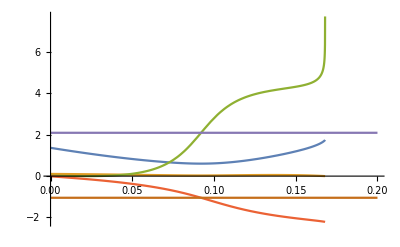

```mathematica
zL:=0;
zR:=0.2;
sol=ParametricNDSolveValue[Join[equations, bcsLeft], {R, r, a, b}, {z, zL, zR},{s},Method->"ExplicitRungeKutta",WorkingPrecision->30,MaxSteps->100000,PrecisionGoal->15,AccuracyGoal->15];
ss=14.328587937819526;
Plot[{sol[ss][[1]][z],sol[ss][[2]][z],sol[ss][[3]][z],sol[ss][[4]][z], a1/2, b1/2},{z, zL,zR}, PlotRange->Full]
```

```mathematica
f1s[s_?NumericQ]:=Function[x,sol[s][[3]][x]]
f2s[s_?NumericQ]:=Function[x,sol[s][[4]][x]]
x1[s_?NumericQ]:=Module[{res},res=FindMinimum[{(f1s[s][x]-a1/2)^2,0<=x<zR},{x,3/4*zR} ];
x/. Last[res]]
x2[s_?NumericQ]:=Module[{res},res=FindMinimum[{(f2s[s][x]-b1/2)^2,0<=x<zR},{x,3/4*zR}];
x/. Last[res]]
res=FindMinimum[{(x1[s]-x2[s])^2,0<=s<=20},{s,10}];
sOpt=s/. Last[res];
res
```

ParametricNDSolveValue::ndsz: At z == 0.173466716301639632614613917912, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At z == 0.173469494090270627736744045834, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolveValue::ndsz: At z == 0.173463938807132550849278440693, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolveValue::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.198252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {0.198252} and/or the interpolation grid is insufficient to compute the value.

FindMinimum::nrnum: The function value (π/3+InterpolatingFunction[{{0,0.1679626266925539}},{5,3,1,{599},{4},0,0,0,0,Automatic,«3»},{{0,«10»}},{{-0.0103648738425715,-5.49470865433293},{-0.0287196390744755,-5.6390123321295},«8»,«589»},{Automatic}][«20»])^2 is not a real number at {x} = {0.198252}.

InterpolatingFunction::dmval: Input value {0.198252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {0.198252} and/or the interpolation grid is insufficient to compute the value.

FindMinimum::nrnum: The function value (π/3+InterpolatingFunction[{{0,0.1679626266925539}},{5,3,1,{599},{4},0,0,0,0,Automatic,«3»},{{0,«10»}},{{-0.0103648738425715,-5.49470865433293},{-0.0287196390744755,-5.6390123321295},«8»,«589»},{Automatic}][«20»])^2 is not a real number at {x} = {0.198252}.

InterpolatingFunction::dmval: Input value {0.198252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {0.198252} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value (π/3+InterpolatingFunction[{{0,0.1679649136557283}},{5,3,1,{599},{4},0,0,0,0,Automatic,«3»},{{0,«10»}},{{-0.0103648738425715,-5.49467314445081},{-0.0287195211054242,-5.638975436903},«8»,«589»},{Automatic}][«19»])^2 is not a real number at {x} = {0.198252}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

{2.23279×10^-10,{s→14.3286}}

```mathematica
{x1[ss], x2[ss]}
```

InterpolatingFunction::dmval: Input value {0.198252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {0.198252} and/or the interpolation grid is insufficient to compute the value.

FindMinimum::nrnum: The function value (π/3+InterpolatingFunction[{{0,0.1679626266925539}},{5,3,1,{599},{4},0,0,0,0,Automatic,«3»},{{0,«10»}},{{-0.0103648738425715,-5.49470865433293},{-0.0287196390744755,-5.6390123321295},«8»,«589»},{Automatic}][«20»])^2 is not a real number at {x} = {0.198252}.

InterpolatingFunction::dmval: Input value {0.198252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {0.198252} and/or the interpolation grid is insufficient to compute the value.

FindMinimum::nrnum: The function value (π/3+InterpolatingFunction[{{0,0.1679626266925539}},{5,3,1,{599},{4},0,0,0,0,Automatic,«3»},{{0,«10»}},{{-0.0103648738425715,-5.49470865433293},{-0.0287196390744755,-5.6390123321295},«8»,«589»},{Automatic}][«20»])^2 is not a real number at {x} = {0.198252}.

{0.0920928,0.0921077}

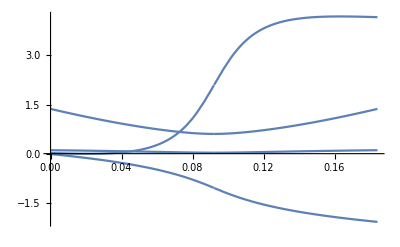

```mathematica
moisei=x1[ss];
Plot[If[z<=moisei, {sol[ss][[1]][z], sol[ss][[2]][z], sol[ss][[3]][z], sol[ss][[4]][z]}, {sol[ss][[1]][2moisei-z], sol[ss][[2]][2moisei-z], 4Pi/3-sol[ss][[3]][2moisei-z],-2Pi/3- sol[ss][[4]][2moisei-z]}], {z, 0, 2moisei}, PlotRange->Full]
```

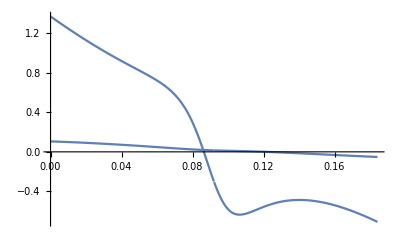

```mathematica
Plot[If[z<=moisei, {Re[sol[ss][[1]][z]*Exp[I*sol[ss][[3]][z]]], Re[sol[ss][[2]][z]*Exp[I*sol[ss][[4]][z]]]}, {Re[sol[ss][[1]][2moisei-z]*Exp[I*(4Pi/3-sol[ss][[3]][2moisei-z])]], Re[sol[ss][[2]][2moisei-z]*Exp[I*(-2Pi/3- sol[ss][[4]][2moisei-z])]]}], {z, 0, 2moisei}, PlotRange->Full]
```

```mathematica
(*Проверка \partial_\mu j^\mu = 0*)
```

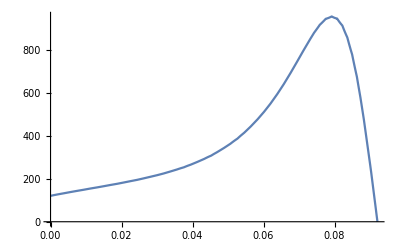

```mathematica
Plot[{2sol[ss][[1]][z](D[sol[ss][[1]][x],x]/.x->z)*(D[sol[ss][[3]][x],x]/.x->z)+(sol[ss][[1]][z])^2(D[sol[ss][[3]][x],{x, 2}]/.x->z)}, {z, 0, moisei}, PlotRange->Full]
```

```mathematica
(*Решение уравнения на A^z для нахождения A, при котором ток сохраняется (при условии A^\mu=0 для любых \mu кроме z)*)
equationOnA:={D[A[z],z]+2/(sol[ss][[1]][z])D[sol[ss][[1]][z],z]*A[z]+2/(sol[ss][[1]][z])D[sol[ss][[1]][z],z]*D[sol[ss][[3]][z],z]+D[sol[ss][[3]][z],{z,2}]==0}
boundCondOnA:={A[zL]==0}
zL:=0;
zR:=moisei;
solOnA=NDSolveValue[Join[equationOnA, boundCondOnA], {A}, {z, zL, zR},Method->"ExplicitRungeKutta",WorkingPrecision->30,MaxSteps->100000,PrecisionGoal->15,AccuracyGoal->15];
```

NDSolveValue::ndsz: At z == 0.167962626692553893993471725427, step size is effectively zero; singularity or stiff system suspected.

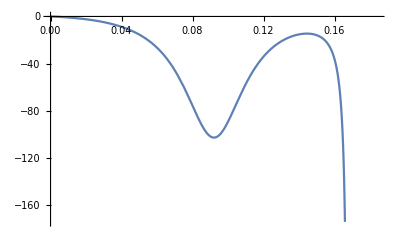

```mathematica
Plot[solOnA[[1]][z],{z, 0,2moisei}]
```

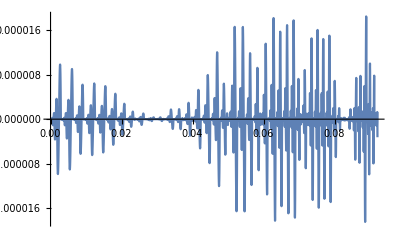

```mathematica
Plot[2sol[ss][[1]][z]sol[ss][[1]]'[z](-sol[ss][[3]]'[z]-solOnA[[1]][z])+(sol[ss][[1]][z])^2(-sol[ss][[3]]''[z]-solOnA[[1]]'[z]), {z, 0, moisei}, PlotRange->Full]
```

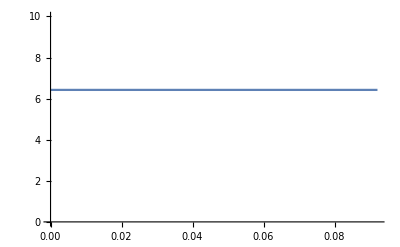

```mathematica
(*При таком A ток:*)
Plot[-2(sol[ss][[1]][z])^2(sol[ss][[3]]'[z]+solOnA[[1]][z]),{z, 0, moisei}, PlotRange->{{0, moisei}, {0, 10}}]
```